```mathematica
(* model predict max *)
tmax0 = 365;

(*Rate of progressing to infectiousness, days*)
daysFromInfectedToInfectious0 = 4;

(*Rate of losing infectiousness or going to the hospital*)
daysUntilNotInfectiousOrHospitalized0 = 5;

(*Rate of leaving hospital for those not going to critical care*)
daysToLeaveHosptialNonCritical0 = 8;

(*Rate of leaving hospital and going to critical care*)
daysTogoToCriticalCare0 = 4;

(*Rate of leaving critical care, weeks*)
daysFromCriticalToRecoveredOrDeceased0 = 10;

(* probabilities of getting pcr confirmations given hospitalized / non-hospitalized resp *)
pPCRH0 = 0.8;
pPCRNH0 = 0.05;

(* How out of date are reports of hospitalizations? *)
daysForHospitalsToReportCases0 = 1;
daysToGetTestedIfNotHospitalized0 = 5.5;
daysToGetTestedIfHospitalized0 = 1.5;

(* the penalty to fatailty rate in the case patients cannot get ICU care *) 
icuOverloadDeathPenalty0 = 2;
 
(* virus start parameters *)
initialInfectionImpulse0 = 12.5;

(*Duration of pulse in force of infection for establishment, days*)
importlength0 = 3;

(*Establishment time, N days before X Cases*)
importtime0 = (31+20);

(* mitigation parameters *)
r0natural0 = 3.1;

(*Fraction of critical patents who pass *)
fractionOfCriticalDeceased0 = 0.4;

USAPopulation = (327.2*10^6);

(* less than 3000 cases in a country the size of the US *)
containmentThresholdRatio0 = 3000/USAPopulation;

(* interpret as: steepness of age depencence*)
medianHospitalizationAge0 = 61;

(* interpret as: steepness of age depencence*)
ageCriticalDependence0 = 3;
ageHospitalizedDependence0 = 5;

(*Probability of 100 year being hospitalized*)
pHospitalized100Yo = 0.25;
(*Probability of 100 year old needing critical care*)
pCriticalGivenHospitalized100Yo = 0.3;

(* percent positive test delay *)
percentPositiveTestDelay0 = 11;

(*Probability of needing critical care*)
pC0 = pCriticalGivenHospitalized100Yo*pHospitalized100Yo;

(*Probability of hospitalization but not critical care*)
pH0 = (1-pCriticalGivenHospitalized100Yo)*pHospitalized100Yo;

(*Probability of not needing care*)
pS0 = 1-(pC0 + pH0);
```

```mathematica
scenario1=<|"id"->"scenario1","distancingDays"->90,"maintain"->True,"name"->"Current"|>;
scenario2=<|"id"->"scenario2","distancingDays"->90,"distancingLevel"->0.4,"maintain"->False,"name"->"Italy"|>;
scenario3=<|"id"->"scenario3","distancingDays"->60,"distancingLevel"->0.11,"maintain"->False,"name"->"Wuhan"|>;
scenario4=<|"id"->"scenario4","distancingDays"->90,"distancingLevel"->1,"maintain"->False,"name"->"Normal"|>;
scenarios={scenario1,scenario2,scenario3,scenario4};
today=QuantityMagnitude[DateDifference[DateList[{2020,1,1}],Today]];
```

```mathematica
(* Assumption here is that age dependence follows a logistic curve -- zero year olds dont require any care, 
100 year olds require significant case, midpoint is the medianHospitalization age *)
infectedCritical[a_,medianHospitalizationAge_,pCLimit_,ageCriticalDependence_] := 
	pCLimit/(1+Exp[-((a-medianHospitalizationAge)/ageCriticalDependence)]);

infectedHospitalized[a_,medianHospitalizationAge_,pHLimit_,ageHospitalizedDependence_] :=
	pHLimit/(1+Exp[-((a-medianHospitalizationAge)/ageHospitalizedDependence)]);

noCare[a_,medianHospitalizationAge_,pCLimit_, pHLimit_,ageCriticalDependence_,ageHospitalizedDependence_] := 
	1-infectedCritical[a, medianHospitalizationAge, pCLimit,ageCriticalDependence]-
	infectedHospitalized[a, medianHospitalizationAge,pHLimit, ageHospitalizedDependence];

stateParams[state_, pCLimit_,pHLimit_,medianHospitalizationAge_,ageCriticalDependence_,ageHospitalizedDependence_]:=Module[{raw,pop,dist,buckets},
raw = stateRawDemographicData[state];
pop = raw["Population"];
dist = raw["Distribution"];
buckets = raw["Buckets"];

(*return a map of per state params to values *)
<|"population"->pop,
"importtime0"->If[!KeyExistsQ[stateImportTime, state],Min[#["day"]&/@Select[parsedData,(#["state"]==state&&#["positive"]>=50)&]] - 20,stateImportTime[state]], (* importtime 20 days before 50 PCR confirmed reached *)
"ventilators"->ventilators[state],
"icuBeds"->stateICUData[state]["icuBeds"],
"staffedBeds"->stateICUData[state]["staffedBeds"],
"bedUtilization"->stateICUData[state]["bedUtilization"],
"hospitalCapacity"->(1-stateICUData[state]["bedUtilization"])*stateICUData[state]["staffedBeds"],
"pS"->Sum[noCare[a, medianHospitalizationAge, pCLimit,pHLimit,ageCriticalDependence,ageHospitalizedDependence ]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}],
"pH"->Sum[infectedHospitalized[a, medianHospitalizationAge, pHLimit,ageHospitalizedDependence]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}],
"pC"->Sum[infectedCritical[a, medianHospitalizationAge, pCLimit,ageCriticalDependence]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}]|>
];
```

```mathematica
Clear[equationsODE,eventsODE,initialConditions,outputODE,dependentVariablesODE,parameters,DeaqParametric,PCRParametric];

evaluateState[state_]:= Module[{
   distancing,params,percentPositiveCase,weekOverWeekWeight,longData,thisStateData,model,fit,
   fitParams,icuCapacity,dataWeights,standardErrors,hospitalizationData,hospitalCapacity,gofMetrics,
   equationsODE,eventsODE,initialConditions,outputODE,dependentVariablesODE,parameters,DeaqParametric,PCRParametric,rms,
rlower,
 rupper,
tlower,
tupper,
replower,
repupper
},


distancing = stateDistancingPrecompute[state]["scenario1"]["distancingFunction"];
percentPositiveCase[t_]:=posInterpMap[state][t];
params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0, ageHospitalizedDependence0];
    icuCapacity=params["icuBeds"]/params["population"];

equationsODE={Sq'[t]==(-distancing[t]*r0natural*(ISq[t]+IHq[t]+ICq[t] )*Sq[t])/daysUntilNotInfectiousOrHospitalized0-est[t]*Sq[t],
   Eq'[t]==(distancing[t]*r0natural*(ISq[t]+IHq[t]+ICq[t] )*Sq[t])/daysUntilNotInfectiousOrHospitalized0+est[t]*Sq[t]-Eq[t]/daysFromInfectedToInfectious0,
    (*Infectious total, not yet PCR confirmed,age indep*)
    ISq'[t]==params["pS"]*Eq[t]/daysFromInfectedToInfectious0-ISq[t]/daysUntilNotInfectiousOrHospitalized0, 
    (*Recovered without needing care*)
    RSq'[t]==ISq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Infected and will need hospital, won't need critical care*)
    IHq'[t]==params["pH"]*Eq[t]/daysFromInfectedToInfectious0-IHq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Going to hospital*)
    HHq'[t]==IHq[t]/daysUntilNotInfectiousOrHospitalized0-HHq[t]/daysToLeaveHosptialNonCritical0,
    (*Reported positive hospital cases*)
    RepHq'[t]==(pPCRH0*HHq'[t])/daysForHospitalsToReportCases0,
    (*Cumulative hospitalized count*)
    EHq'[t]==IHq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Recovered after hospitalization*)
    RHq'[t]==HHq[t]/daysToLeaveHosptialNonCritical0,
    (*pcr confirmation*)
    PCR'[t]==reportingLag*(((pPCRNH0*percentPositiveCase[t]*(ISq[t]+IHq[t]+ICq[t] ))/daysToGetTestedIfNotHospitalized0+(pPCRH0*percentPositiveCase[t]*HHq[t])/daysToGetTestedIfHospitalized0)),
    (*Infected, will need critical care*)
    ICq'[t]==params["pC"]*Eq[t]/daysFromInfectedToInfectious0-ICq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Hospitalized,
    need critical care*)
    HCq'[t]==ICq[t]/daysUntilNotInfectiousOrHospitalized0-HCq[t]/daysTogoToCriticalCare0,
    (*Entering critical care*)
    CCq'[t]==HCq[t]/daysTogoToCriticalCare0-CCq[t]/daysFromCriticalToRecoveredOrDeceased0,
    (*Dying*)
 Deaq'[t]==CCq[t]*If[CCq[t]>=icuCapacity,2*fractionOfCriticalDeceased0,fractionOfCriticalDeceased0]/daysFromCriticalToRecoveredOrDeceased0,
    (*Leaving critical care*)
    RCq'[t]==CCq[t]*(1-fractionOfCriticalDeceased0)/daysFromCriticalToRecoveredOrDeceased0,
    
    est'[t]==0
}/.Thread[{r0natural,importtime,reportingLag}->fromLog/@{logR0Natural,logImportTime,logReportingLag}];
eventsODE = {
    WhenEvent[t>=importtime,est[t]->Exp[-initialInfectionImpulse0]],
    WhenEvent[t>importtime+importlength0,est[t]->0]
}/.Thread[{r0natural,importtime,reportingLag}->fromLog/@{logR0Natural,logImportTime,logReportingLag}];
initialConditions = {Sq[0]==1,Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RepHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,Deaq[0]==0,est[0]==0,PCR[0]==0,EHq[0]==0};
outputODE = {Deaq, PCR};
dependentVariablesODE = {Deaq, PCR, 
 RSq,RHq, RCq,
RepHq, Sq, Eq, ISq, IHq, HHq, ICq, EHq, HCq, CCq, est};
parameters = {logR0Natural,logImportTime,logReportingLag};
{DeaqParametric,PCRParametric}= {Deaq, PCR}/.ParametricNDSolve[{equationsODE, 
  eventsODE, 
  initialConditions
}, outputODE, 
{t,0,tmax0}, 
parameters,
DependentVariables->dependentVariablesODE,
Method->{"DiscontinuityProcessing"->False}
];

{rlower,
 rupper,
tlower,
tupper,
replower,
repupper}=getBounds[state];

thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];

longData=Select[Join[
	  {1,#["day"],If[TrueQ[#["death"]==Null],0,(#["death"]/params["population"])//N]}&/@thisStateData,
	  {2,#["day"],(#["positive"]/params["population"])//N}&/@thisStateData
	],#[[3]]>0&];
model[r0natural_,importtime_,reportingLag_,c_][t_]:=Piecewise[{{
DeaqParametric[r0natural,importtime,reportingLag][t],c==1},{PCRParametric[r0natural,importtime,reportingLag][t] ,c==2}}];

     weekOverWeekWeight=.75;
dataWeights=(weekOverWeekWeight^(#[[1]]/7)(params["population"]#[[3]])^-1)&/@longData;
fit=NonlinearModelFit[
    longData,
    {model[r0natural,importtime,reportingLag,c][t],
    Log[rlower]<=r0natural<=Log[rupper],
    Log[tlower]<=importtime<=Log[tupper],
    Log[replower]<= reportingLag<=Log[repupper]},{{r0natural,Log[(rlower+rupper)/2]}, {importtime,Log[(tlower+tupper)/2]}, {reportingLag,Log[(replower+repupper)/2]}},{c,t},
Method->{"NMinimize",Method->"SimulatedAnnealing"},Weights->dataWeights
(*EvaluationMonitor:>Print["r0natural=",Exp[r0natural],".    importtime=",Exp[importtime], ".    reportingLag=",Exp[reportingLag]]*)];

fitParams=Exp[#]&/@KeyMap[ToString[#]&, Association[fit["BestFitParameters"]]];

{fitParams,
fit,
DeaqParametric,
PCRParametric,
longData
}
]
```

```mathematica
Clear[fitState];
fitState[state_,rlower_:2.5,rupper_:3.8,tlower_:40,tupper_:60,replower_:4,repupper_:6]:=Module[{fitParams,fit,DeaqParametric,PCRParametric,longData},
  {fitParams,
fit,
DeaqParametric,
PCRParametric,
longData
}=evaluateState[state,rlower,rupper,tlower,tupper,replower,repupper]//Quiet;

Column[{
Show[
ListLogPlot[Cases[longData,{#, t_,c_}:>{t,c}]&/@{1,2},ImageSize->500,PlotRange->{{1,150},{0,0.0005}}],
LogPlot[{
DeaqParametric[Log[fitParams["r0natural"]],Log[fitParams["importtime"]],Log[fitParams["reportingLag"]]][t],PCRParametric[Log[fitParams["r0natural"]],Log[fitParams["importtime"]],Log[fitParams["reportingLag"]]][t]},
{t,1,150},ImageSize->500]],
Row[{fromLog@fit["ParameterTable"]//Quiet,fit["ANOVATable"]//Quiet}]
}]
]
```

```mathematica
getBounds["CA"]
```

{2.9,3.1,45,47,5.5,6.5}

```mathematica
fitStartingOverrides=<|
"PA"-><|"rlower"->3.1,"rupper"->4.4,"tlower"->55,"tupper"->70,"replower"->4,"repupper"->6|>,
"CO"-><|"rlower"->3.1,"rupper"->4.4,"tlower"->40,"tupper"->60,"replower"->3,"repupper"->4.6|>,
"MD"-><|"rlower"->3.1,"rupper"->4.6,"tlower"->40,"tupper"->60,"replower"->3,"repupper"->5|>,
"TX"-><|"rlower"->3.1,"rupper"->4.8,"tlower"->40,"tupper"->60,"replower"->4.4,"repupper"->5|>,
"WA"-><|"rlower"->2.5,"rupper"->4.8,"tlower"->35,"tupper"->44,"replower"->3,"repupper"->5|>,
"CT"-><|"rlower"->3.4,"rupper"->4.2,"tlower"->47,"tupper"->55,"replower"->3,"repupper"->5|>,
"OH"-><|"rlower"->3.4,"rupper"->4.2,"tlower"->47,"tupper"->55,"replower"->3,"repupper"->4|>,
"VA"-><|"rlower"->3.4,"rupper"->4.2,"tlower"->47,"tupper"->53,"replower"->5,"repupper"->6|>
|>;
```

```mathematica
testCaseStates={"CA","VA","FL","CO", "MD","TX","WA","OR", "PA", "CT", "OH", "VT"};
```

```mathematica
getBounds[state_]:=Module[{},
If[MemberQ[Keys[fitStartingOverrides],state],
{fitStartingOverrides[state]["rlower"],fitStartingOverrides[state]["rupper"],fitStartingOverrides[state]["tlower"],fitStartingOverrides[state]["tupper"],fitStartingOverrides[state]["replower"],fitStartingOverrides[state]["reepupper"]},
{2.5,3.8,40,60,4,6}]
];
```

```mathematica
fitStateOverRide[state_]:=Apply[fitState,If[MemberQ[Keys[fitStartingOverrides],state],{state,fitStartingOverrides[state]["rlower"],fitStartingOverrides[state]["rupper"],fitStartingOverrides[state]["tlower"],fitStartingOverrides[state]["tupper"],fitStartingOverrides[state]["replower"],fitStartingOverrides[state]["repupper"]},{state,2.5,3.8,40,60,4,6}]];
```

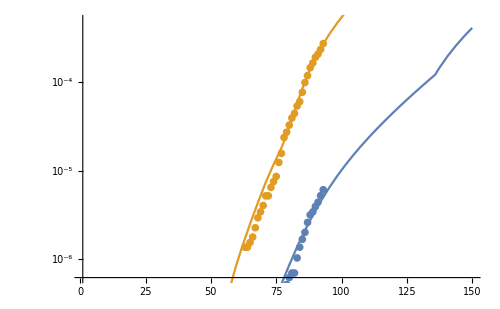
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.04985 | 0.0484217 | 62.9852 | 4.88788×10^-50
ⅇ^importtime | 46.9631 | 0.705376 | 66.5789 | 2.98271×10^-51
ⅇ^reportingLag | 6.44602 | 0.683647 | 9.42886 | 9.21108×10^-13 | DF | SS | MS
Model | 3 | 4.4833×10^-11 | 1.49443×10^-11
Error | 51 | 5.61407×10^-13 | 1.1008×10^-14
Uncorrected Total | 54 | 4.53944×10^-11 | 
Corrected Total | 53 | 4.43624×10^-11 |

```mathematica
fitStateOverRide["CA"]
```

```mathematica
Grid[Partition[Column[{Text[#],fitStateOverRide[#]}]&/@testCaseStates[[1;4]],4]]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Grid[Partition[CO,4]]

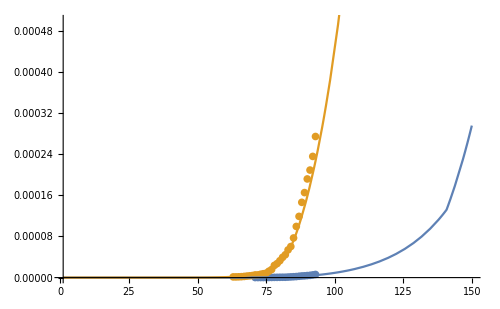
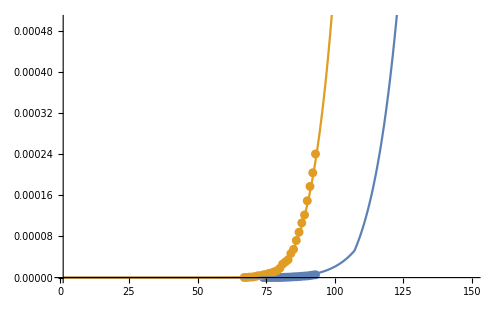
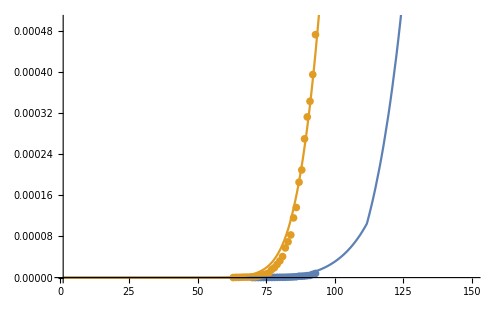
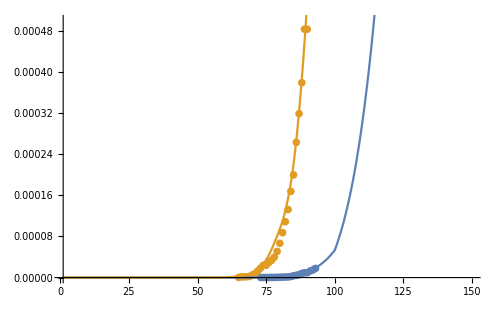
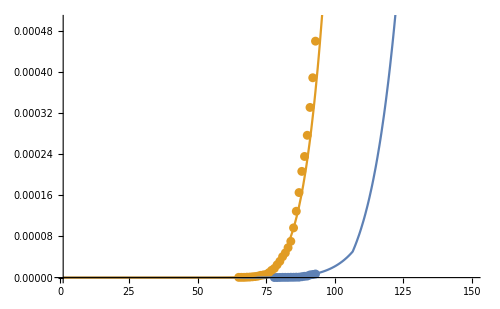
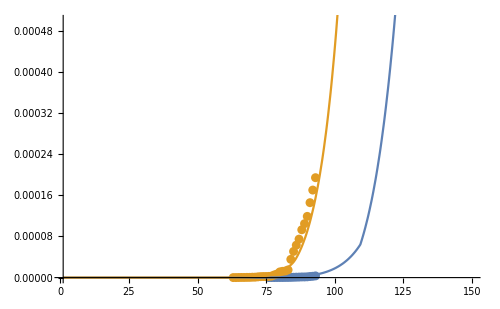
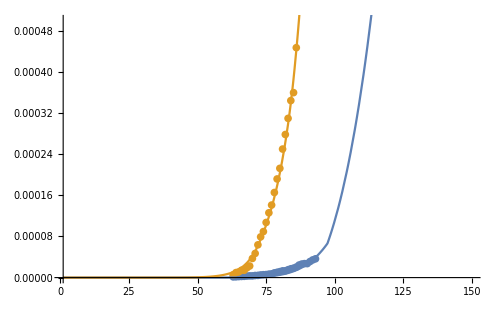
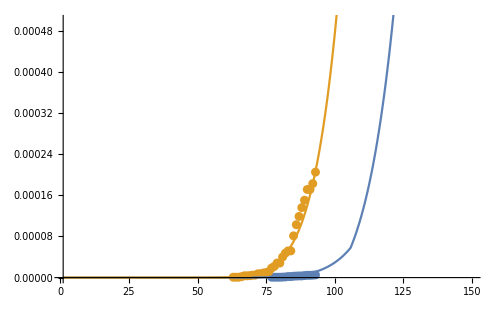
CA
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 2.97063 | 0.0803803 | 36.9573 | 1.73003×10^-38
ⅇ^importtime | 46.598 | 1.076 | 43.3067 | 6.81154×10^-42
ⅇ^reportingLag | 5.90415 | 1.04531 | 5.64823 | 7.2561×10^-7 | DF | SS | MS
Model | 3 | 4.41234×10^-11 | 1.47078×10^-11
Error | 51 | 1.27094×10^-12 | 2.49204×10^-14
Uncorrected Total | 54 | 4.53944×10^-11 | 
Corrected Total | 53 | 4.43624×10^-11 |  | VA
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.8946 | 0.0824007 | 47.2641 | 2.35505×10^-39
ⅇ^importtime | 52.4686 | 0.594304 | 88.2857 | 3.64678×10^-51
ⅇ^reportingLag | 5.09433 | 0.499698 | 10.1948 | 3.67217×10^-13 | DF | SS | MS
Model | 3 | 1.58865×10^-10 | 5.29551×10^-11
Error | 44 | 3.05479×10^-12 | 6.9427×10^-14
Uncorrected Total | 47 | 1.6192×10^-10 | 
Corrected Total | 46 | 1.58271×10^-10 |  | FL
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.77514 | 0.135106 | 27.942 | 5.46999×10^-33
ⅇ^importtime | 50.9362 | 1.21348 | 41.9754 | 8.70682×10^-42
ⅇ^reportingLag | 5.38061 | 1.15967 | 4.63977 | 0.0000239492 | DF | SS | MS
Model | 3 | 1.13779×10^-10 | 3.79264×10^-11
Error | 52 | 1.62179×10^-11 | 3.11883×10^-13
Uncorrected Total | 55 | 1.29997×10^-10 | 
Corrected Total | 54 | 1.28467×10^-10 |  | CO
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.37591 | 0.124351 | 35.19 | 2.01248×10^-35
ⅇ^importtime | 50.9362 | 0.992633 | 51.3142 | 6.30701×10^-43
ⅇ^reportingLag | 4.10084 | 0.81926 | 5.00555 | 8.25589×10^-6 | DF | SS | MS
Model | 3 | 7.86983×10^-10 | 2.62328×10^-10
Error | 47 | 4.12594×10^-11 | 8.7786×10^-13
Uncorrected Total | 50 | 8.28242×10^-10 | 
Corrected Total | 49 | 8.17836×10^-10 | 
MD
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.52046 | 0.172755 | 26.1669 | 1.25823×10^-27
ⅇ^importtime | 55.2672 | 0.992352 | 55.6931 | 5.40029×10^-41
ⅇ^reportingLag | 3.71941 | 0.765034 | 4.86176 | 0.0000166553 | DF | SS | MS
Model | 3 | 3.91083×10^-10 | 1.30361×10^-10
Error | 42 | 1.79733×10^-11 | 4.27935×10^-13
Uncorrected Total | 45 | 4.09056×10^-10 | 
Corrected Total | 44 | 4.01071×10^-10 |  | TX
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.44947 | 0.226092 | 19.6799 | 4.88481×10^-24
ⅇ^importtime | 56.0852 | 1.14187 | 49.117 | 2.13915×10^-41
ⅇ^reportingLag | 4.71438 | 0.982416 | 4.79876 | 0.0000172133 | DF | SS | MS
Model | 3 | 3.48265×10^-11 | 1.16088×10^-11
Error | 46 | 3.74865×10^-12 | 8.14924×10^-14
Uncorrected Total | 49 | 3.85751×10^-11 | 
Corrected Total | 48 | 3.80679×10^-11 |  | WA
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.47623 | 0.0549911 | 63.2144 | 6.63687×10^-56
ⅇ^importtime | 40.2949 | 0.723688 | 55.6799 | 1.04967×10^-52
ⅇ^reportingLag | 4.98093 | 0.485139 | 10.267 | 9.49331×10^-15 | DF | SS | MS
Model | 3 | 1.11174×10^-9 | 3.7058×10^-10
Error | 59 | 1.6588×10^-11 | 2.81153×10^-13
Uncorrected Total | 62 | 1.12833×10^-9 | 
Corrected Total | 61 | 1.05361×10^-9 |  | OR
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.53589 | 0.108148 | 32.6951 | 5.29831×10^-33
ⅇ^importtime | 48.7015 | 0.931342 | 52.2917 | 6.08985×10^-42
ⅇ^reportingLag | 5.09518 | 0.543853 | 9.36866 | 3.85107×10^-12 | DF | SS | MS
Model | 3 | 3.81356×10^-10 | 1.27119×10^-10
Error | 45 | 1.32784×10^-11 | 2.95076×10^-13
Uncorrected Total | 48 | 3.94635×10^-10 | 
Corrected Total | 47 | 3.64144×10^-10 | 
PA
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.3683 | 0.493687 | 8.84833 | 3.79345×10^-11
ⅇ^importtime | 55.6058 | 2.94672 | 18.8704 | 3.97514×10^-22
ⅇ^reportingLag | 5.47485 | 3.48032 | 1.57309 | 0.123202 | DF | SS | MS
Model | 3 | 1.93736×10^-10 | 6.45788×10^-11
Error | 42 | 6.07382×10^-11 | 1.44615×10^-12
Uncorrected Total | 45 | 2.54475×10^-10 | 
Corrected Total | 44 | 2.52337×10^-10 |  | CT
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.2 | 0.258265 | 16.2624 | 3.14556×10^-19
ⅇ^importtime | 49.824 | 2.84726 | 17.4989 | 2.38712×10^-20
ⅇ^reportingLag | 4.86052 | 3.06558 | 1.58551 | 0.120725 | DF | SS | MS
Model | 3 | 1.53901×10^-9 | 5.13002×10^-10
Error | 40 | 3.85981×10^-10 | 9.64952×10^-12
Uncorrected Total | 43 | 1.92499×10^-9 | 
Corrected Total | 42 | 1.90136×10^-9 |  | OH
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.06871 | 0.164017 | 24.8067 | 4.46029×10^-25
ⅇ^importtime | 54.1227 | 1.45583 | 37.1767 | 1.72422×10^-31
ⅇ^reportingLag | 3.20779 | 1.00987 | 3.17644 | 0.00295714 | DF | SS | MS
Model | 3 | 1.30879×10^-10 | 4.36264×10^-11
Error | 38 | 1.46988×10^-11 | 3.8681×10^-13
Uncorrected Total | 41 | 1.45578×10^-10 | 
Corrected Total | 40 | 1.42469×10^-10 |  | VT
-Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.79097 | 0.164388 | 23.0611 | 2.46777×10^-24
ⅇ^importtime | 46.2317 | 1.78314 | 25.9272 | 3.36488×10^-26
ⅇ^reportingLag | 5.59004 | 1.66747 | 3.35242 | 0.00179068 | DF | SS | MS
Model | 3 | 6.44891×10^-9 | 2.14964×10^-9
Error | 39 | 6.64116×10^-10 | 1.70286×10^-11
Uncorrected Total | 42 | 7.11302×10^-9 | 
Corrected Total | 41 | 6.62433×10^-9 |

```mathematica
Grid[Partition[Column[{Text[#],fitStateOverRide[#]}]&/@testCaseStates,4]]
```

```mathematica
fitAbsolute=NonlinearModelFit[longData,model,{{r0natural, r0natural0}, {importtime, params["importtime0"]-5},  {k, 1}},{t,c}];
fitAbsoluteParams=KeyMap[ToString[#]&, Association[fitAbsolute["BestFitParameters"]]]
{deathresidabs, pcrresidabs}=resuidualsMultiPlot[fitAbsolute,longDataAbsolute];
Row[{
ListPlot[deathresidabs, Filling->Axis,ImageSize->300],
ListPlot[pcrresidabs,Filling->Axis,ImageSize->300],
Manipulate[
Column[{
Row[{
Show[
ListPlot[Cases[longDataAbsolute,{t_,#,c_}:>{t,c}]&/@{1,2},PlotRange->{{60,120},{0,0.00002}}],
Plot[{
DeaqParametric[r0natural,importtime,k][t]-DeaqParametric[r0natural,importtime,k][t-1],PCRParametric[r0natural,importtime,k][t] - PCRParametric[r0natural,importtime,k][t -1]},
{t,1,120}]]},ImageSize->300]
}],
{{r0natural,fitAbsoluteParams["r0natural"]},2,6},{{importtime,fitAbsoluteParams["importtime"]}, 40,100},{{k,fitAbsoluteParams["k"]}, 1,5}
]}]
```

NonlinearModelFit::fitd: First argument longData in NonlinearModelFit is not a list or a rectangular array.

KeyMap::invak: The argument Association[fitAbsolute[BestFitParameters]] is not a valid Association.

KeyMap[ToString[#1]&,Association[fitAbsolute[BestFitParameters]]]

Set::shape: Lists {deathresidabs,pcrresidabs} and resuidualsMultiPlot[NonlinearModelFit[longData,model,{{r0natural,3.1},{importtime,-5+params[importtime0]},{k,1}},{t,c}],longDataAbsolute] are not the same shape.

ListPlot::lpn: deathresidabs is not a list of numbers or pairs of numbers.

ListPlot::lpn: pcrresidabs is not a list of numbers or pairs of numbers.

KeyMap::argx: KeyMap called with 2 arguments; 1 argument is expected.

General::stop: Further output of KeyMap::argx will be suppressed during this calculation.

ListPlot[deathresidabs,Filling→Axis,ImageSize→300]ListPlot[pcrresidabs,Filling→Axis,ImageSize→300]

KeyMap::invak: The argument Association[fitAbsolute[BestFitParameters]] is not a valid Association.

KeyMap::argx: KeyMap called with 2 arguments; 1 argument is expected.

KeyMap::invak: The argument Association[fitAbsolute[BestFitParameters]] is not a valid Association.

KeyMap::argx: KeyMap called with 2 arguments; 1 argument is expected.

KeyMap::invak: The argument Association[fitAbsolute[BestFitParameters]] is not a valid Association.

General::stop: Further output of KeyMap::invak will be suppressed during this calculation.

KeyMap::argx: KeyMap called with 2 arguments; 1 argument is expected.

General::stop: Further output of KeyMap::argx will be suppressed during this calculation.

```mathematica
ClearAll[residualsPlot]
residualsPlot[fit_FittedModel] := Module[{width = 4 72},
  GraphicsGrid[{{
     ListPlot[Thread[{First /@ fit["Data"], fit["FitResiduals"]}],
      FrameLabel -> {"time (d)", "FitResiduals"},
      Filling -> Axis,
      ImageSize -> width
      ],
     ListPlot[Thread[{fit["PredictedResponse"], fit["FitResiduals"]}],
      FrameLabel -> {"PredictedResponse", "FitResiduals"},
      Filling -> Axis,
      ImageSize -> width
      ]
     }},
   Spacings -> Scaled[0.05]
   ]
  ]
```

```mathematica
ListPlot[deathresid]
ListPlot[pcrresid]
```

ListPlot::lpn: deathresid is not a list of numbers or pairs of numbers.

ListPlot[deathresid]

ListPlot::lpn: pcrresid is not a list of numbers or pairs of numbers.

ListPlot[pcrresid]

```mathematica
resuidualsMultiPlot[fit_, data_]:=Module[{lengthOfDeathData,deathData, pcrData, resid, deathResid, pcrResid, deathResideTime, pcrResideTime},
lengthOfDeathData=Length[Select[data,#[[2]]==1&]];
deathData={#[[1]],#[[3]]}&/@data[[1;;lengthOfDeathData]];
pcrData={#[[1]],#[[3]]}&/@data[[lengthOfDeathData+1;;Length[data]]];
resid=fit["FitResiduals"];
deathResid = resid[[1;;lengthOfDeathData]];
pcrResid=resid[[lengthOfDeathData+1;;Length[data]]];
deathResideTime=MapIndexed[{#1[[1]],deathResid[[#2]][[1]]}&,deathData];
pcrResideTime=MapIndexed[{#1[[1]],pcrResid[[#2]][[1]]}&,pcrData];

{Transpose@{deathData[[All,1]],(deathData[[All,2]]-deathResideTime[[All,2]])/deathData[[All,2]]},
Transpose@{pcrData[[All,1]],(pcrData[[All,2]]-pcrResideTime[[All,2]])/pcrData[[All,2]]}}
]
```

```mathematica
{deathresid, pcrresid}= resuidualsMultiPlot[fit,longData];
```

Select::normal: Nonatomic expression expected at position 1 in Select[longData,#1⟦2⟧==1&].

Part::take: Cannot take positions 1 through 2 in longData.

Part::partd: Part specification longData⟦1⟧ is longer than depth of object.

Part::partd: Part specification longData⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of 1;;2 does not exist.

Part::pkspec1: The expression {1,(1;;2)⟦3⟧} cannot be used as a part specification.

Part::take: Cannot take positions 3 through 0 in longData.

Part::partd: Part specification longData⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of 3;;0 does not exist.

Part::pkspec1: The expression {3,(3;;0)⟦3⟧} cannot be used as a part specification.

Part::take: Cannot take positions 1 through 2 in fit[FitResiduals].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part {3,3} of {longData⟦1⟧,FitResiduals} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression (1;;2)⟦3⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {longData,{(-1+longData⟦3⟧⟦(1;;2)⟦3⟧⟧)/(longData⟦3⟧⟦(1;;2)⟦3⟧⟧),(-1+longData⟦3⟧⟦(1;;2)⟦3⟧⟧)/(longData⟦3⟧⟦(1;;2)⟦3⟧⟧)}} cannot be transposed.

Transpose::nmtx: The first two levels of {longData⟦1⟧⟦3⟧,(-FitResiduals⟦3⟧+longData⟦3⟧⟦(3;;0)⟦3⟧⟧)/(longData⟦3⟧⟦(3;;0)⟦3⟧⟧)} cannot be transposed.

```mathematica
ListPlot[deathresid]
ListPlot[pcrresid]
```

Transpose::nmtx: The first two levels of {longData,{(-1.+longData⟦3⟧⟦(1;;2)⟦3⟧⟧)/(longData⟦3⟧⟦(1;;2)⟦3⟧⟧),(-1.+longData⟦3⟧⟦(1;;2)⟦3⟧⟧)/(longData⟦3⟧⟦(1;;2)⟦3⟧⟧)}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{longData,{(-1.+longData⟦3⟧⟦Span[«2»]⟦3⟧⟧)/(longData⟦3⟧⟦Span[«2»]⟦3⟧⟧),(-1.+longData⟦3⟧⟦Span[«2»]⟦3⟧⟧)/(longData⟦3⟧⟦Span[«2»]⟦3⟧⟧)}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{longData,{(-1+longData⟦3⟧⟦(1;;2)⟦3⟧⟧)/(longData⟦3⟧⟦(1;;2)⟦3⟧⟧),(-1+longData⟦3⟧⟦(1;;2)⟦3⟧⟧)/(longData⟦3⟧⟦(1;;2)⟦3⟧⟧)}}]]

Transpose::nmtx: The first two levels of {longData⟦1⟧⟦3⟧,(-1. FitResiduals⟦3⟧+longData⟦3⟧⟦(3;;0)⟦3⟧⟧)/(longData⟦3⟧⟦(3;;0)⟦3⟧⟧)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{longData⟦1⟧⟦3⟧,(-1. FitResiduals⟦3⟧+longData⟦3⟧⟦(3;;0)⟦3⟧⟧)/(longData⟦3⟧⟦(3;;0)⟦3⟧⟧)}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{longData⟦1⟧⟦3⟧,(-FitResiduals⟦3⟧+longData⟦3⟧⟦(3;;0)⟦3⟧⟧)/(longData⟦3⟧⟦(3;;0)⟦3⟧⟧)}]]

```mathematica
fit["FitResiduals"]
```

fit[FitResiduals]

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
toLog[x_] := Log[x]
```

```mathematica
ClearAll[fromLog]
SetAttributes[fromLog, HoldAll]; 
fromLog[y_] := Exp[y]
fromLog[(fit_)["ParameterTable"]] := 
	fit["ParameterTable"] /. Grid[array_, options___] :> Module[{a = array}, 
		a[[2;;]] = Replace[a[[2;;]], 
			{p_, v_, se_, t_, pr_} :> {fromLog[p], fromLog[v], fromLog[v]*se, t, pr}, {1}]; 
		a = Replace[a, {p_, (v_)?NumberQ, se_, t_, pr_} :> {p, v, se, v/se, 
			(N[#1, 6] & )[TwoSidedPValue /. StudentTPValue[v/se, 
			fit["ANOVATableDegreesOfFreedom"][[2]], TwoSided -> True]]}, {1}]; 
		Grid[a, options]
		]
```

```mathematica
toLogit[x_] := Log[x/(1-x)]
fromLogit[y_]:=Exp[y]/(1 + Exp[y])
```

```mathematica
Clear[equationsODE,eventsODE,initialConditions,outputODE,dependentVariablesODE,parameters,DeaqParametric,PCRParametric];

evaluateState[state_,rlower_,rupper_,tlower_,tupper_,replower_,repupper_]:= Module[{
   distancing,params,percentPositiveCase,weekOverWeekWeight,longData,thisStateData,model,fit,
   fitParams,icuCapacity,dataWeights,standardErrors,hospitalizationData,hospitalCapacity,gofMetrics,
   equationsODE,eventsODE,initialConditions,outputODE,dependentVariablesODE,parameters,DeaqParametric,PCRParametric,rms
},


distancing = stateDistancingPrecompute[state]["scenario1"]["distancingFunction"];
percentPositiveCase[t_]:=posInterpMap[state][t];
params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0, ageHospitalizedDependence0];
    icuCapacity=params["icuBeds"]/params["population"];

equationsODE={Sq'[t]==(-distancing[t]*r0natural*(ISq[t]+IHq[t]+ICq[t] )*Sq[t])/daysUntilNotInfectiousOrHospitalized0-est[t]*Sq[t],
   Eq'[t]==(distancing[t]*r0natural*(ISq[t]+IHq[t]+ICq[t] )*Sq[t])/daysUntilNotInfectiousOrHospitalized0+est[t]*Sq[t]-Eq[t]/daysFromInfectedToInfectious0,
    (*Infectious total, not yet PCR confirmed,age indep*)
    ISq'[t]==params["pS"]*Eq[t]/daysFromInfectedToInfectious0-ISq[t]/daysUntilNotInfectiousOrHospitalized0, 
    (*Recovered without needing care*)
    RSq'[t]==ISq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Infected and will need hospital, won't need critical care*)
    IHq'[t]==params["pH"]*Eq[t]/daysFromInfectedToInfectious0-IHq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Going to hospital*)
    HHq'[t]==IHq[t]/daysUntilNotInfectiousOrHospitalized0-HHq[t]/daysToLeaveHosptialNonCritical0,
    (*Reported positive hospital cases*)
    RepHq'[t]==(pPCRH0*HHq'[t])/daysForHospitalsToReportCases0,
    (*Cumulative hospitalized count*)
    EHq'[t]==IHq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Recovered after hospitalization*)
    RHq'[t]==HHq[t]/daysToLeaveHosptialNonCritical0,
    (*pcr confirmation*)
    PCR'[t]==reportingLag*(((pPCRNH0*percentPositiveCase[t]*(ISq[t]+IHq[t]+ICq[t] ))/daysToGetTestedIfNotHospitalized0+(pPCRH0*percentPositiveCase[t]*HHq[t])/daysToGetTestedIfHospitalized0)),
    (*Infected, will need critical care*)
    ICq'[t]==params["pC"]*Eq[t]/daysFromInfectedToInfectious0-ICq[t]/daysUntilNotInfectiousOrHospitalized0,
    (*Hospitalized,
    need critical care*)
    HCq'[t]==ICq[t]/daysUntilNotInfectiousOrHospitalized0-HCq[t]/daysTogoToCriticalCare0,
    (*Entering critical care*)
    CCq'[t]==HCq[t]/daysTogoToCriticalCare0-CCq[t]/daysFromCriticalToRecoveredOrDeceased0,
    (*Dying*)
 Deaq'[t]==CCq[t]*If[CCq[t]>=icuCapacity,2*fractionOfCriticalDeceased0,fractionOfCriticalDeceased0]/daysFromCriticalToRecoveredOrDeceased0,
    (*Leaving critical care*)
    RCq'[t]==CCq[t]*(1-fractionOfCriticalDeceased0)/daysFromCriticalToRecoveredOrDeceased0,
    
    est'[t]==0
}/.Thread[{r0natural,importtime,reportingLag}->fromLog/@{logR0Natural,logImportTime,logReportingLag}];
eventsODE = {
    WhenEvent[t>=importtime,est[t]->Exp[-initialInfectionImpulse0]],
    WhenEvent[t>importtime+importlength0,est[t]->0]
}/.Thread[{r0natural,importtime,reportingLag}->fromLog/@{logR0Natural,logImportTime,logReportingLag}];
initialConditions = {Sq[0]==1,Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RepHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,Deaq[0]==0,est[0]==0,PCR[0]==0,EHq[0]==0};
outputODE = {Deaq, PCR};
dependentVariablesODE = {Deaq, PCR, 
 RSq,RHq, RCq,
RepHq, Sq, Eq, ISq, IHq, HHq, ICq, EHq, HCq, CCq, est};
parameters = {logR0Natural,logImportTime,logReportingLag};
{DeaqParametric,PCRParametric,RSqParametric,RHqParametric,RCqParametric,RepHqParametric,SqParametric,EqParametric,ISqParametric,IHqParametric,HHqParametric,ICqParametric,EHqParametric,HCqParametric,CCqParametric,estParametric}= {Deaq, PCR, 
 RSq,RHq, RCq,
RepHq, Sq, Eq, ISq, IHq, HHq, ICq, EHq, HCq, CCq, est}/.ParametricNDSolve[{equationsODE, 
  eventsODE, 
  initialConditions
}, outputODE, 
{t,0,tmax0}, 
parameters,
DependentVariables->dependentVariablesODE,
Method->{"DiscontinuityProcessing"->False}
];


thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];

longData=Select[Join[
	  {1,#["day"],If[TrueQ[#["deathIncrease"]==Null],0,(#["deathIncrease"]/params["population"])//N]}&/@thisStateData,
	  {2,#["day"],(#["positiveIncrease"]/params["population"])//N}&/@thisStateData
	],#[[3]]>0&];
model[r0natural_,importtime_,reportingLag_,c_][t_]:=Piecewise[{{
DeaqParametric[r0natural,importtime,reportingLag][t]-DeaqParametric[r0natural,importtime,reportingLag][t-1],c==1},{PCRParametric[r0natural,importtime,reportingLag][t] - PCRParametric[r0natural,importtime,reportingLag][t -1],c==2}}];

weekOverWeekWeight=.75;

dataWeights=(weekOverWeekWeight^(#[[1]]/7)(params["population"]#[[3]])^-1)&/@longData;
fit=NonlinearModelFit[
    longData,
    {model[r0natural,importtime,reportingLag,c][t],
    Log[rlower]<=r0natural<=Log[rupper],
    Log[tlower]<=importtime<=Log[tupper],
    Log[replower]<= reportingLag<=Log[repupper]},{{r0natural,Log[(rlower+rupper)/2]}, {importtime,Log[(tlower+tupper)/2]}, {reportingLag,Log[(replower+repupper)/2]}},{c,t},
Method->{"NMinimize",Method->"SimulatedAnnealing"},Weights->dataWeights];
fitParams=Exp[#]&/@KeyMap[ToString[#]&, Association[fit["BestFitParameters"]]];

{fitParams,
fit,
DeaqParametric,
PCRParametric,
longData
}
]
```

```mathematica
Clear[fitState];
fitState[state_,rlower_:2.5,rupper_:3.8,tlower_:40,tupper_:60,replower_:4,repupper_:6]:=Module[{fitParams,fit,DeaqParametric,PCRParametric,longData},
  {fitParams,
fit,
DeaqParametric,
PCRParametric,
longData
}=evaluateState[state,rlower,rupper,tlower,tupper,replower,repupper]//Quiet;

Column[{
Show[
ListLogPlot[Cases[longData,{#, t_,c_}:>{t,c}]&/@{1,2},ImageSize->500,PlotRange->{{60,120},{0,0.0002}}],
LogPlot[{
DeaqParametric[Log[fitParams["r0natural"]],Log[fitParams["importtime"]],Log[fitParams["reportingLag"]]][t]-DeaqParametric[Log[fitParams["r0natural"]],Log[fitParams["importtime"]],Log[fitParams["reportingLag"]]][t-1],PCRParametric[Log[fitParams["r0natural"]],Log[fitParams["importtime"]],Log[fitParams["reportingLag"]]][t] - PCRParametric[Log[fitParams["r0natural"]],Log[fitParams["importtime"]],Log[fitParams["reportingLag"]]][t -1]},
{t,1,120},ImageSize->500]],
Row[{fromLog@fit["ParameterTable"]//Quiet,fit["ANOVATable"]//Quiet}]
}]
]
```

```mathematica
fitStartingOverrides=<|
"PA"-><|"rlower"->3.1,"rupper"->4.4,"tlower"->55,"tupper"->70,"replower"->4,"repupper"->6|>,
"CO"-><|"rlower"->3.1,"rupper"->4.4,"tlower"->40,"tupper"->60,"replower"->3,"repupper"->4.6|>,
"MD"-><|"rlower"->3.1,"rupper"->4.6,"tlower"->40,"tupper"->60,"replower"->3,"repupper"->5|>,
"TX"-><|"rlower"->3.1,"rupper"->4.8,"tlower"->40,"tupper"->60,"replower"->4.4,"repupper"->5|>,
"WA"-><|"rlower"->2.5,"rupper"->4.8,"tlower"->35,"tupper"->44,"replower"->3,"repupper"->5|>,
"CT"-><|"rlower"->3.4,"rupper"->4.2,"tlower"->47,"tupper"->55,"replower"->3,"repupper"->5|>,
"OH"-><|"rlower"->3.4,"rupper"->4.2,"tlower"->47,"tupper"->55,"replower"->3,"repupper"->4|>
|>;
```

```mathematica
getBounds[state_]:=Module[{},
If[MemberQ[Keys[fitStartingOverrides],state],
{fitStartingOverrides[state]["rlower"],fitStartingOverrides[state]["rupper"],fitStartingOverrides[state]["tlower"],fitStartingOverrides[state]["tupper"],fitStartingOverrides[state]["replower"],fitStartingOverrides[state]["reepupper"]},
{2.5,3.8,40,60,4,6}]
];
```

```mathematica
If[MemberQ[Keys[fitStartingOverrides],#],{#,fitStartingOverrides[#]["rlower"],fitStartingOverrides[#]["rupper"],fitStartingOverrides[#]["tlower"],fitStartingOverrides[#]["tupper"],fitStartingOverrides[#]["replower"],fitStartingOverrides[#]["reepuppere"]},{#,2.5,3.8,40,60,4,6}]
```

{#1,2.5,3.8,40,60,4,6}

```mathematica
fitStateOverRide[state_]:=Apply[fitState,If[MemberQ[Keys[fitStartingOverrides],state],{state,fitStartingOverrides[state]["rlower"],fitStartingOverrides[state]["rupper"],fitStartingOverrides[state]["tlower"],fitStartingOverrides[state]["tupper"],fitStartingOverrides[state]["replower"],fitStartingOverrides[state]["repupper"]},{state,2.5,3.8,40,60,4,6}]];
```